## Решение задачи ЛО графическим методом

-x_1-3 x_2≥-15
2 x_1+x_2≤17
-2 x_1-3 x_2≥-23
x_1≥0,x_2≥0
f=-40 x_1-30 x_2→min

## Решение

-x_1-3 x_2=-15
2 x_1+x_2=17
-2 x_1-3 x_2=-23:> 1)]x_1=0,x_2=5;]x_2=0,x_1=15;
2)]x_1=0,x_2=17;]x_2=0,x_1=8.5;
3)]x_1=0,x_2=23/3;]x_2=0,x_1=11.5;
Grad f: x_1 | x_2
0 | 0
-40 | -30; 
] f = 120: x_1 | x_2
0 | -4
-3 | 0;

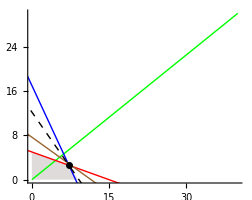
-Graphics-
Градиент -f:  RGBColor[0, 1, 0]
1){0;5},{15;0}:  RGBColor[1, 0, 0]
2){0;17},{8.5;0}:  RGBColor[0, 0, 1]
3){0;23/3},{11.5;0}:  RGBColor[0.6, 0.4, 0.2]
f = 120: - - - - -

```mathematica
Grid[{{Show[{Graphics[{RGBColor[0.4,0.3,0.3,0.2],Polygon[{{0,0},{0,5},{36/5,13/5},{9,0}}]}],Graphics[{Red,InfiniteLine[{{0,5},{15,0}}]}],Graphics[{Blue,InfiniteLine[{{0,17},{8.5,0}}]}],Graphics[{Brown,InfiniteLine[{{0,23/3},{11.5,0}}]}],Graphics[{Green,Line[{{0,0},{40,30}}]}],Graphics[{Black,Dashed,InfiniteLine[{{0,-4},{-3,0}}]}],Graphics[{Black,Dashed,InfiniteLine[{{36/5,13/5},{51/5,-7/5}}]}],Graphics[{PointSize[0.02],Point[{36/5,13/5}]}]},Axes->True,AxesStyle->Directive[Black,12]]},
{Text[Style[RGBColor[0, 1, 0]"Градиент -f: ",14,Black]]},
{Text[Style[RGBColor[1, 0, 0]"1){0;5},{15;0}: ",14,Black]]},
{Text[Style[RGBColor[0, 0, 1]"2){0;17},{8.5;0}: ",14,Black]]},
{Text[Style[RGBColor[0.6, 0.4, 0.2]"3){0;23/3},{11.5;0}: ",14,Black]]},
{Text[Style["f = 120: - - - - -",14,Black]]}}]
```

2 ∩ 1: -x_1-3 x_2=-15
2 x_1+x_2=17  :>   -x_1-51+6 x_1=-15
x_2=17-2 x_1  :>  x_1=36/5
x_2=13/5;
f = -40*36/5-30*13/5 = -366